```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]]
```

```mathematica
operatorHadamard = QuantumMatrixOperation["Hadamard"];
```

```mathematica
operatorRotate = QuantumMatrixOperation[{"RotZ",Pi/4}];
```

```mathematica
operatorCNOT = QuantumMatrixOperation["CNOT"];
```

```mathematica
operatorFourier = QuantumMatrixOperation[{"Fourier",2}];
```

```mathematica
operatorFourier1 = QuantumMatrixOperation[{"Fourier",1}];
```

```mathematica
states ={QuantumFiniteDimensionalState[{{1,0},{0,1}}],QuantumFiniteDimensionalState[{{1,0},{1,0}}],QuantumFiniteDimensionalState[{{1,0},{0,1}}]};
```

```mathematica
fixStupidity[expression_]:=((expression)//.{Sqrt[x_]->x,Power[x_,Rational[1,n_Integer]]->x,Power[x_,Rational[-1,n_Integer]]->1/x})
```

```mathematica
getState[cell_]:= QuantumPartialTr[cell,{2}]
```

```mathematica
getControlled[cell_]:=QuantumPartialTr[cell,{1}]
```

```mathematica
generateEntangledState[]:=QuantumFiniteDimensionalState[{"PhiPlus"}]
```

```mathematica
entangledpair = generateEntangledState[];
```

```mathematica
entangledMeasurement = QuantumMeasurement["Observable"-> "SigmaX"];
```

```mathematica
(* create QFDS, of state qubit (j+1) and entangled states *)
(* apply CNOT on state qubit and first entangled qubit *)
(* apply Hadamard on state qubit *)
(* measure state qubit and second entangled qubit *)
```

```mathematica
entangledThreeState[pair_,states_,j_Integer]:=
QuantumFiniteDimensionalState[fixStupidity[{Normal[getState[states[[j+1]]]["StateVector"]],Normal[pair["StateVector"]]}]]/;j≠Length[states]

entangledThreeState[pair_,states_,j_Integer]:=
QuantumFiniteDimensionalState[fixStupidity[{Normal[getState[states[[1]]]["StateVector"]],Normal[pair["StateVector"]]}]]/;j===Length[states]
```

```mathematica
chooseTeleportationOperation[pair_,states_,j_Integer]:=
Flatten[{QuantumEvaluate[{1}-> entangledMeasurement,
QuantumEvaluate[{1}-> operatorHadamard,QuantumEvaluate[{1,2}-> operatorCNOT,entangledThreeState[pair,states,j]]]],QuantumEvaluate[{2}-> entangledMeasurement,QuantumEvaluate[{1,2}-> operatorCNOT,entangledThreeState[pair,states,j]]]
}]
```

```mathematica
applyControlOperation[pair_,states_,j_Integer]:=
Module[{answer=chooseTeleportationOperation[pair,states,j]},
Which[
answer==={-1,-1},
QuantumEvaluate[{1}-> operatorFourier1,getControlled[states[[j]]]],
answer==={-1,1},
QuantumEvaluate[{1}-> operatorCNOT,getControlled[states[[j]]]],
answer==={1,-1},
QuantumEvaluate[{1}-> operatorCNOT,getControlled[states[[j]]]],
answer==={1,1},
QuantumEvaluate[{1}-> operatorHadamard,getControlled[states[[j]]]]]]
```

```mathematica
createNewCell[j_Integer,states_,pair_,operator_]:= 
QuantumEvaluate[{1,2}-> operator,QuantumFiniteDimensionalState[fixStupidity[
{Normal[applyControlOperation[pair,states,j]["StateVector"]],Normal[getState[states[[j]]]["StateVector"]]}]]]
```

```mathematica
nextState[operator_,pair_,states_]:= createNewCell[#,states,pair,operator]&/@Range[Length[states]]
```

```mathematica
allStates[operator_,pair_,states_,n_Integer]:= NestList[nextState[operator,pair,#]&,states,n]
```

```mathematica
(* in CA, finding disorder and randomness from initial structure is a surprise, in QCA finding order is a surprise? *)
```

```mathematica
separateStates[states_]:= Map[{Normal[getState[#]["StateVector"]],Normal[getControlled[#]["StateVector"]]}&,states]
separateAllStates[states_]:= separateStates[#]&/@states
```

```mathematica
getColour[com_]:= RGBColor[N[Re[com],10],0,N[Im[com],10]]/;Re[com]≥ 0&&Im[com]≥0
getColour[com_]:= Blend[{ColorNegate[RGBColor[Abs[N[Re[com],10]],0,0]],RGBColor[0,0,N[Im[com],10]]}]/;Re[com]≤ 0&&Im[com]≥0
getColour[com_]:= Blend[{RGBColor[Abs[N[Re[com],10]],0,0],ColorNegate[RGBColor[0,0,N[Im[com],10]]]}]/;Re[com]≥ 0&&Im[com]≤0
getColour[com_]:= Blend[{ColorNegate[RGBColor[Abs[N[Re[com],10]],0,0]],ColorNegate[RGBColor[0,0,N[Im[com],10]]]}]/;Re[com]≤ 0&&Im[com]≤0
```

```mathematica
colourQubit[qubit_]:= {getColour[qubit⟦1⟧],getColour[qubit⟦2⟧]}
```

```mathematica
colourQubit[{1,0}];
```

```mathematica
colourQubit[{0,I}];
```

```mathematica
colourQubit[{-1,0}];
```

```mathematica
colourQubit[{0,-I}];
```

```mathematica
colourCell[cell_]:= {colourQubit[cell⟦1⟧],colourQubit[cell⟦2⟧]}
```

```mathematica
colourState[state_]:=Map[colourCell,state]
```

```mathematica
colourAll[allstates_]:=Map[colourState, allstates]
```

```mathematica
showQubit[qubit_]:= Rotate[ArrayPlot[{colourQubit[qubit]},Frame-> False],3Pi/2]
```

```mathematica
showQubit[{1,0}];
```

```mathematica
showCell[cell_]:= Row[{showQubit[cell⟦1⟧],showQubit[cell⟦2⟧]}]
```

```mathematica
showCell[{{1,0},{0,1}}];
```

```mathematica
showState[state_]:=Map[showCell,state]
```

```mathematica
showAll[allState_]:= Grid[Map[showState,allState]]
```

```mathematica
QuantumCellularAutomata[operator_,initialstate_,steps_Integer]:= showAll[separateAllStates[allStates[operator,entangledpair,initialstate,steps]]]
```

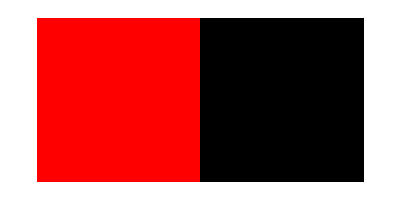
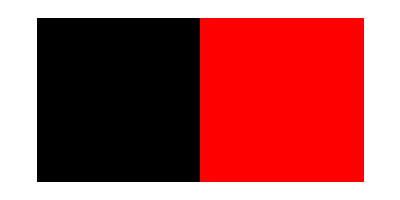
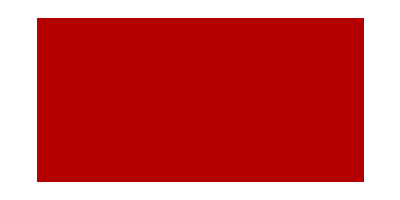
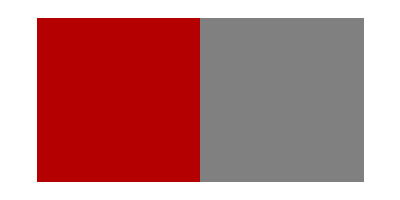
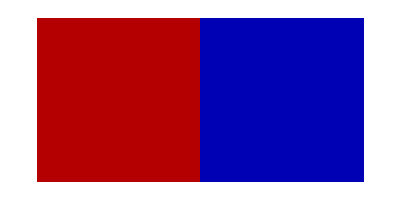
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
QuantumCellularAutomata[operatorFourier,{QuantumFiniteDimensionalState[{{1,0},{0,1}}],QuantumFiniteDimensionalState[{{1,0},{0,1}}],QuantumFiniteDimensionalState[{{1,0},{1,0}}],QuantumFiniteDimensionalState[{{1,0},{0,1}}],QuantumFiniteDimensionalState[{{1,0},{0,1}}]},100]
```

```mathematica
workstate = entangledThreeState[entangledpair, states, 1]
```

QuantumFiniteDimensionalState[…]

```mathematica
doCNOT = QuantumEvaluate[{1,2}-> operatorCNOT,workstate]
```

QuantumFiniteDimensionalState[…]

```mathematica
doHadamard = QuantumEvaluate[{1}-> operatorHadamard, doCNOT]
```

QuantumFiniteDimensionalState[…]

```mathematica
measuredStateQubit = QuantumEvaluate[{1}-> entangledMeasurement,doHadamard]
```

{-1}

```mathematica
measuredEntangledQubit = QuantumEvaluate[{2}-> entangledMeasurement, doHadamard]
```

{1}

```mathematica
doHadamard
```

QuantumFiniteDimensionalState[…]

```mathematica
QuantumPartialTr[doHadamard,{3}]
```

QuantumFiniteDimensionalState[…]

```mathematica
workstate = {getState[states[[2]]],entangledpair}
```

{QuantumFiniteDimensionalState[…],QuantumFiniteDimensionalState[…]}